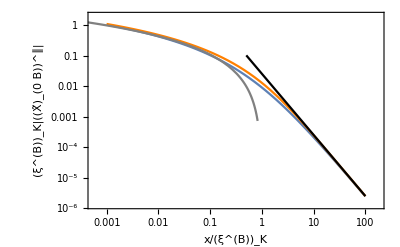

```mathematica
(*For the magnetic case there are two scales and the curves cannot be scaled onto eachother*)
f[ϕ_,x_]:=Abs[Exp[Exp[I ϕ]x]Gamma[0,Exp[I ϕ]x]/(2π)]^2
p1=LogLogPlot[{f[0,x]},{x,0.001,100},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Frame->True,Axes->False,FrameLabel->{"x/(ξ^(B))_K","(ξ^(B))_K|((X̃)_(0  B))^∥|"},PlotLegends->Placed[{"|((X̃)_(0  B))^∥(B=0)|"},{Left,Bottom}]];
p2=LogLogPlot[{f[π/2,x]},{x,0.001,100},PlotLegends->Placed[{"|((X̃)_(0  B))^∥(B≠0)|"},{Left,Bottom}],PlotStyle->{Orange}];
p3=LogLogPlot[Log[x]^2/(5 π^2 ),{x,0.0001,1},PlotStyle->{Gray}];
p4=LogLogPlot[1/(4 π^2 x^2),{x,0.5,100},PlotStyle->{Black}];
Show[p1,p2,p3,p4]
```

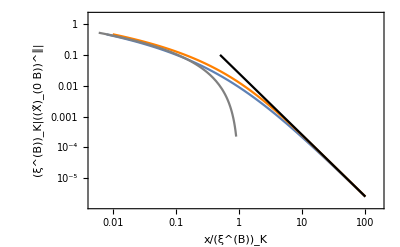

```mathematica
f[ϕ_,x_]:=Abs[Exp[Exp[I ϕ]x]Gamma[0,Exp[I ϕ]x]/(2π)]^2
p1=LogLogPlot[{f[0,x]},{x,0.008,100},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Frame->True,Axes->False,FrameLabel->{"x/(ξ^(B))_K","(ξ^(B))_K|((X̃)_(0  B))^∥|"}];
p2=LogLogPlot[{f[π/2,x]},{x,0.01,100},PlotStyle->{Orange}];
p3=LogLogPlot[Log[x]^2/(5 π^2 ),{x,0.006,1},PlotStyle->{Gray}];
p4=LogLogPlot[1/(4 π^2 x^2),{x,0.5,100},PlotStyle->{Black}];
Show[p1,p2,p3,p4]
```

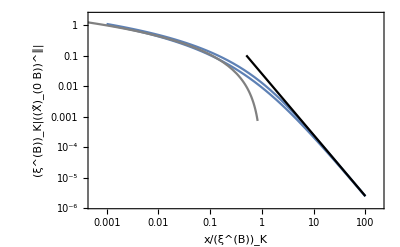

```mathematica
f[ϕ_,x_]:=Abs[Exp[Exp[I ϕ]x]Gamma[0,Exp[I ϕ]x]/(2π)]^2
p1=LogLogPlot[{f[0,x]},{x,0.001,100},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Frame->True,Axes->False,FrameLabel->{"x/(ξ^(B))_K","(ξ^(B))_K|((X̃)_(0  B))^∥|"}];
p2=LogLogPlot[{f[π/2,x]},{x,0.001,100}];
p3=LogLogPlot[Log[x]^2/(5 π^2 ),{x,0.0001,1},PlotStyle->{Gray}];
p4=LogLogPlot[1/(4 π^2 x^2),{x,0.5,100},PlotStyle->{Black}];
Show[p1,p2,p3,p4]
```